```mathematica
k1[ε_,ky_]:=√(√(ε^2-Eg^2)-ky^2);
k2[ε_,ky_]:=√(√(ε^2-Eg^2)+ky^2);
q1[ε_,ky_,V_]:=Sign[ε-V]√(√((ε-V)^2-Eg^2)-ky^2)/;√((ε-V)^2-Eg^2)-ky^2≥0;
q1[ε_,ky_,V_]:=ⅈ√(ky^2-√((ε-V)^2-Eg^2))/;√((ε-V)^2-Eg^2)-ky^2<0;
q2[ε_,ky_,V_]:=√(√((ε-V)^2-Eg^2)+ky^2);
current1[ε_,ky_]:=k1[ε,ky](ε-Eg)√(ε^2-Eg^2);
current2[ε_,ky_,V_]:=q1[ε,ky,V](ε-V-Eg)√((ε-V)^2-Eg^2)/;√((ε-V)^2-Eg^2)-ky^2≥0;
current2[ε_,ky_,V_]:=0/;√((ε-V)^2-Eg^2)-ky^2<0;

ψ1R[ε_,ky_,x_]:=({{-(k1[ε,ky]-ⅈ ξ ky)^2}, {ε-Eg}})ⅇ^(ⅈ k1[ε,ky] x);
ψ1L[ε_,ky_,x_]:=({{-(k1[ε,ky]+ⅈ ξ ky)^2}, {ε-Eg}})ⅇ^(-ⅈ k1[ε,ky] x);
ψ2R[ε_,ky_,x_]:=({{(k2[ε,ky]-ξ ky)^2}, {ε-Eg}})ⅇ^(-k2[ε,ky] x);
ψ2L[ε_,ky_,x_]:=({{(k2[ε,ky]+ξ ky)^2}, {ε-Eg}})ⅇ^(k2[ε,ky] x);


φ1R[ε_,ky_,V_,x_]:=({{-(q1[ε,ky,V]-ⅈ ξ ky)^2}, {ε-V-Eg}})ⅇ^(ⅈ q1[ε,ky,V] x);
φ1L[ε_,ky_,V_,x_]:=({{-(q1[ε,ky,V]+ⅈ ξ ky)^2}, {ε-V-Eg}})ⅇ^(-ⅈ q1[ε,ky,V] x);
φ2R[ε_,ky_,V_,x_]:=({{(q2[ε,ky,V]-ξ ky)^2}, {ε-V-Eg}})ⅇ^(-q2[ε,ky,V] x);
φ2L[ε_,ky_,V_,x_]:=({{(q2[ε,ky,V]+ξ ky)^2}, {ε-V-Eg}})ⅇ^(q2[ε,ky,V] x);
Eq[ε_,ky_,V_]:={
ψ1R[ε,ky,0]+r1*ψ1L[ε,ky,0]+r2*ψ2L[ε,ky,0]==t1*φ1R[ε,ky,V,0]+t2*φ2R[ε,ky,V,0],

ⅈ k1[ε,ky]ψ1R[ε,ky,0]-ⅈ k1[ε,ky]r1*ψ1L[ε,ky,0]+r2 k2[ε,ky]ψ2L[ε,ky,0]==ⅈ q1[ε,ky,V]t1*φ1R[ε,ky,V,0]-t2 q2[ε,ky,V]φ2R[ε,ky,V,0]
};
Print["Complete"]
```

Complete

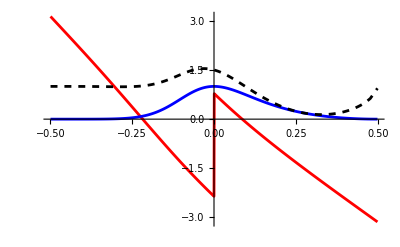

```mathematica
dk=800;
εmax=20;(*The given energy E*)
V=2εmax;(*The electrostatic potential V*)
ξ=1;(*The valley index, 1 for K valley and -1 for K` valley*)
Eg=εmax Cos[ArcTan[εmax/(V-εmax)]];(*The energy gap Δ*)
result=Table[NSolve[Eq[εmax,ky,V],{r1,r2,t1,t2}],{ky,-(εmax^2-Eg^2)^(1/4)(1-1/(dk)^2),(εmax^2-Eg^2)^(1/4)(1-1/(dk)^2),2(εmax^2-Eg^2)^(1/4)/(dk+1/(dk-1))}];
R1=Flatten[r1/.result];
T1=Flatten[t1/.result];
cu=Table[current2[εmax,ky,V]/current1[εmax,ky],{ky,-(εmax^2-Eg^2)^(1/4)(1-1/(dk)^2),(εmax^2-Eg^2)^(1/4)(1-1/(dk)^2),2(εmax^2-Eg^2)^(1/4)/(dk+1/(dk-1))}];
T=Table[Abs[T1[[i]]]^2*Abs[cu[[i]]],{i,1,dk+1}];
axis=Table[ArcSin[ky/(εmax^2-Eg^2)^(1/4)]/Pi,{ky,-(εmax^2-Eg^2)^(1/4)(1-1/(dk)^2),(εmax^2-Eg^2)^(1/4)(1-1/(dk)^2),2(εmax^2-Eg^2)^(1/4)/(dk+1/(dk-1))}];
dataT=Table[{axis[[i]],T[[i]]},{i,1,dk+1}];(*Data of Fig. 2*)
dataR=Table[{axis[[i]],Arg[R1[[i]]]},{i,1,dk+1}];(*Data of Fig. 5*)
data=Table[{axis[[i]],R[[i]]+T[[i]]},{i,1,dk+1}];
Show[
ListPlot[dataR,PlotRange->All,PlotStyle->Red,Joined->True],
ListPlot[dataT,PlotRange->All,PlotStyle->Blue,Joined->True],
ListPlot[data,PlotRange->All,PlotStyle->{Black,Dashed},Joined->True],PlotRange->All]
```

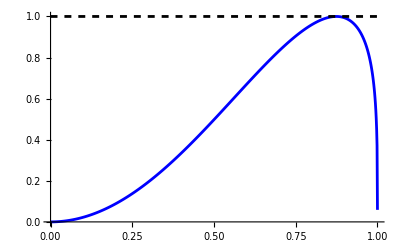

```mathematica
dk=800;
εmax=20;(*The given energy E*)
V=2.8εmax;(*The electrostatic potential V*)
ξ=1;(*The valley index, 1 for K valley and -1 for K` valley*)
result=Table[NSolve[Eq[εmax,0,V],{r1,r2,t1,t2}],{Eg,0,εmax(1-1/(dk)^2),εmax/(dk+1/(dk-1))}];
R1=Flatten[r1/.result];
T1=Flatten[t1/.result];
cu=Table[current2[εmax,0,V]/current1[εmax,0],{Eg,0,εmax(1-1/(dk)^2),εmax/(dk+1/(dk-1))}];
R=Table[Abs[R1[[i]]]^2,{i,1,dk+1}];
T=Table[Abs[T1[[i]]]^2*Abs[cu[[i]]],{i,1,dk+1}];
axis=Table[Eg/εmax,{Eg,0,εmax(1-1/(dk)^2),εmax/(dk+1/(dk-1))}];
dataR=Table[{axis[[i]],(*Arg[R1[[i]]]*)R[[i]]},{i,1,dk+1}];
dataT=Table[{axis[[i]],T[[i]]},{i,1,dk+1}];
data=Table[{axis[[i]],R[[i]]+T[[i]]},{i,1,dk+1}];
Show[
(*ListPlot[dataR,PlotRange->All,PlotStyle->Red,Joined->True],*)
ListPlot[dataT,PlotRange->All,PlotStyle->Blue,Joined->True],
ListPlot[data,PlotRange->All,PlotStyle->{Black,Dashed},Joined->True],PlotRange->All]
```